# disLocate - Mathematica Package: (d)etecting (i)ntermolecular (s)tructure (Locate)d at particle positions

## Load the disLocate.m Package into Mathematica:

### 1. Install Package: Menu Bar > File > Install... > Type [Package] Source: [From File...] Name: [disLocate] > [OK]

#### Click the Blue Cell and Press the Two Buttons: “Shift” + “Enter”

```mathematica
<<disLocate`
disLocateVersion
```

1.2017-08-04.thesis

#### Note: Make sure this line produces a version number before continuing

## Select and Import the Data Files

### 2. Run all Examples by clicking: Menu Bar > Evaluation > Evaluate Entire Notebook

### NOTE: Make sure this notebook is in the same directory as the data folder: micelle_data/

```mathematica
dir=NotebookDirectory[]<>"micelle_data/";
SetDirectory[dir];
```

```mathematica
images={-Graphics-,-Graphics-,-Graphics- ,-Graphics- };
```

```mathematica
xylene2000=Import[dir<>"2000rpm/Result 2000rpm 1um.csv","CSV"][[2;;,3;;4]];
xylene4000=Import[dir<>"4000rpm/Result 4000rpm 1um.csv","CSV"][[2;;,3;;4]];
xylene6000=Import[dir<>"6000rpm/Result 6000rpm 1um.csv","CSV"][[2;;,3;;4]];
xylene8000=Import[dir<>"8000rpm/Result 8000rpm 1um.csv","CSV"][[2;;,3;;4]];
```

```mathematica
xyXyleneList={xylene2000,xylene4000,xylene6000,xylene8000};
nameList={"2000rpm","4000rpm","6000rpm","8000rpm"};
```

## Voronoi Tessellations - Area Distributions

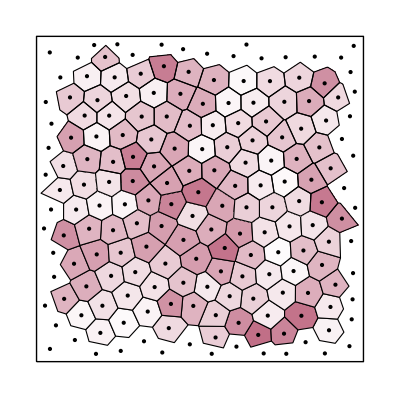
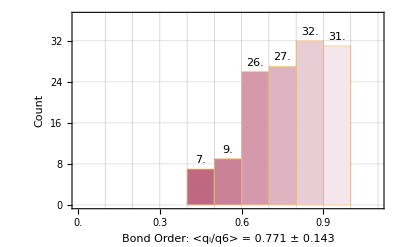

```mathematica
(*  Basic Plot for the Voronoi Tessellation                      *)
(*  Returns the Image of the Tiles and the Histogram of the data *)

PlotVoronoiTessellations@xylene2000
```

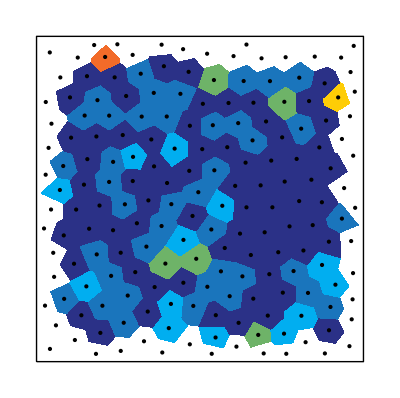
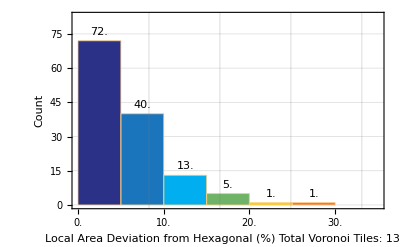
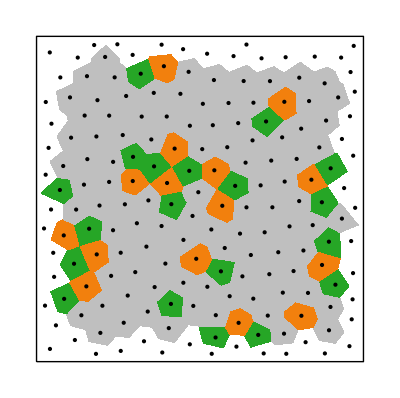
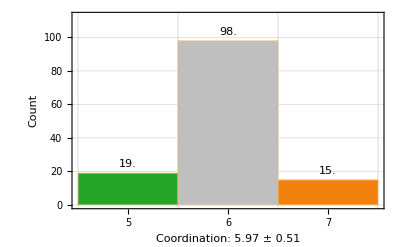
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
(* Additional Option #1 - type *)
(* Change the colour scheme of the Voronoi Tiles *)

PlotVoronoiTessellations[xylene2000,type-> #]&/@{"vor","bop","coord"}
```

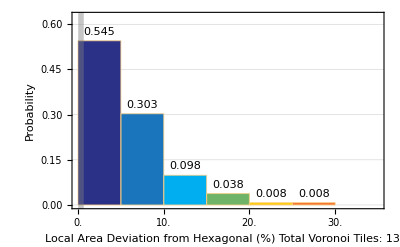
{-Graphics-,-Graphics-}

```mathematica
(* Additional Option #2 - stats *)
(* Instead of Counting the Number of tiles, the Probability can be used. *)

PlotVoronoiTessellations[xylene2000,type-> "vor",stats-> "Probability"]
```

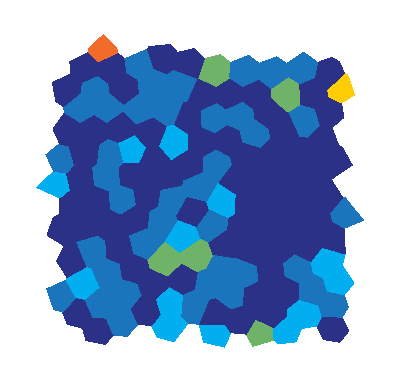
{-Graphics-,-Graphics-}

```mathematica
(* Additional Option #3 - points *)
(* Remove the points and lines to give it a more "stained glass" look *)

PlotVoronoiTessellations[xylene2000,type-> "vor",points-> False]
```

```mathematica
(* Additional Option #4 - raster and scalebar *)
(* a) Change vector graphics to pixelated version - easier to copy/paste *)
(* b) Add the scalebar beside the Voronoi tessellation  *)


PlotVoronoiTessellations[xylene2000,type-> "vor",scalebar->True,raster-> True]
```

{-Graphics-,-Graphics-}

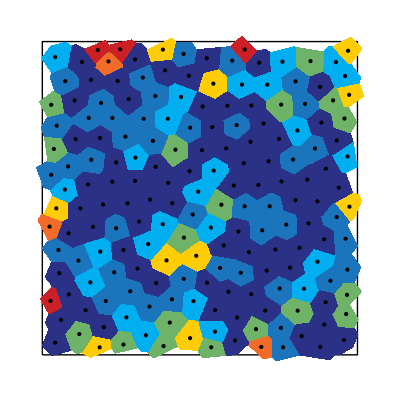
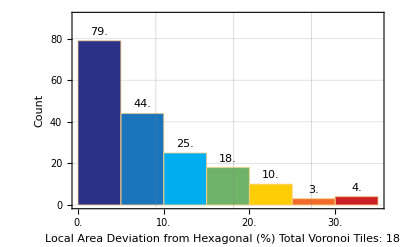
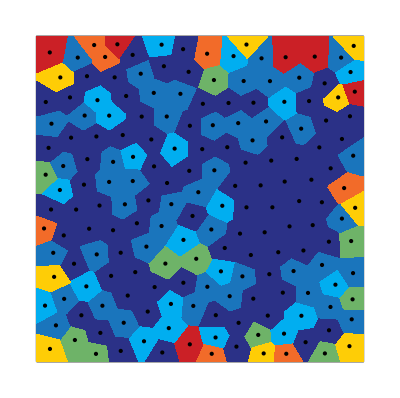
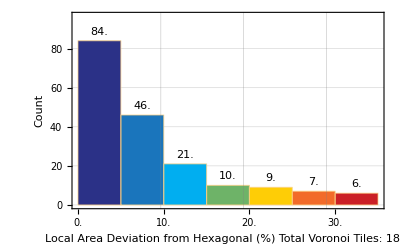
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
(* Additional Option #5 - boundary *)
(* Change the routine to sample points outside the edge *)
(* - noedge: removes any tiles that extend/touch the box *)
(* - pbc:  Applies Periodic boundaries to the edge, total tile areas will total the box area *)
(* - image:  Places image charge particles outside so that the Voronoi tiles clip to the box *)

(* WARNING: type->"vor" depends on the global number density which changes with more particles *)

PlotVoronoiTessellations[xylene2000,type-> "vor",boundary-> #] &/@{"noedge","pbc","image"}
```

```mathematica
(*  Overlay the Nanoparticle Images with the Voronoi Tessellation:  *)
(* a) Image Dimensions tells how many pixels the image is  *)
ImageDimensions[images[[1]]]

(* b) Rescale the points by:  image/box  size  *)
vor=PlotVoronoiTessellations[(410/1000)* xylene2000][[1]];

(* c) The double ImageReflect is needed because the jpeg image {0,0} starts at the top left... *)
(*     ...while xy data starts in the bottom left as the origin.  *)
ImageReflect@Show[{ImageReflect[images[[1]]],vor  }]
```

{410,410}

-Graphics-

```mathematica
(* Scale Bars can be called individually *)
ScaleBars[#]&/@{"voronoi","bop","coord"}
```

{,,}

## Pair Correlation Function - Distance between Particles

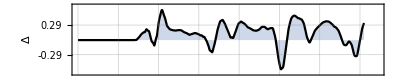
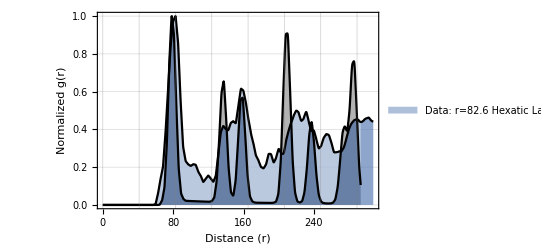

```mathematica
(*  Basic Plot for the Pair Correlation Function                 *)
(*  Returns the Plot of the first-peak normalized g(r) thats Smoothed + Hexatic Lattice *)
(* May take some time to complete:  (1-2 mins for large data sets) *)


PlotPairCorrelationFunction@xylene2000
```

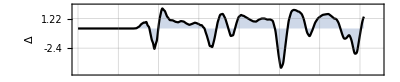
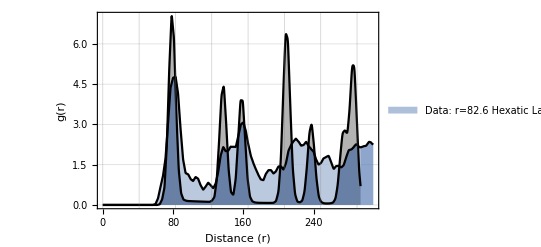

```mathematica
(* Additional Option #1 - normalized *)
(* Remove the normalization of the first peak to see the Absolute Value of g(r)  *)

PlotPairCorrelationFunction[xylene2000,normalized-> False]
```

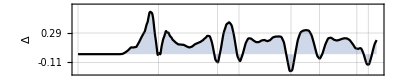
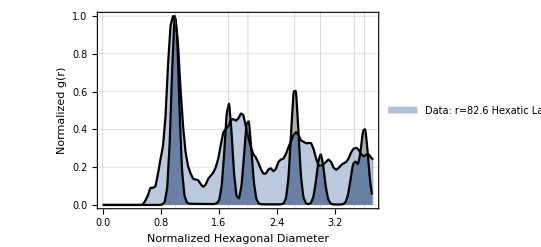
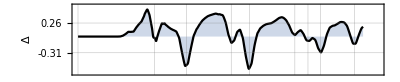
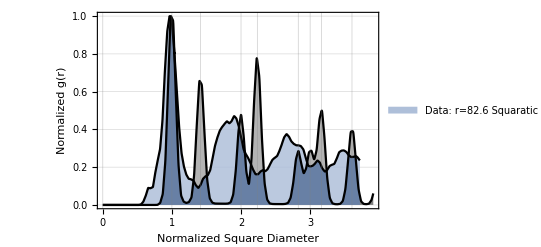

```mathematica
(*     Additional Option #2 - lattice                           *)
(*     Normalizes the x-axis to the expected diameter           *)
(*     Can choose the Reference Lattice:  "hex"  or "square"    *)
PlotPairCorrelationFunction[xylene2000,lattice-> #]&/@{"hex","square"}
```

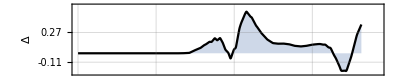
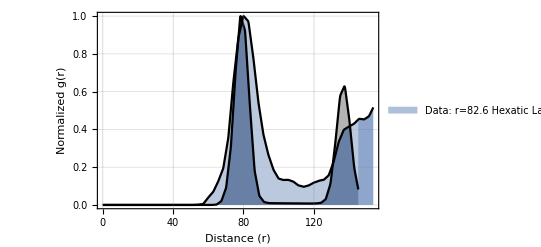
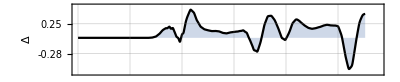
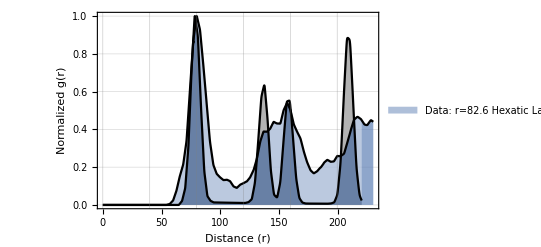

```mathematica
(*     Additional Option #3 - shells                            *)
(*     Vary the plotting distance with this parameter           *)
(*     Default Value = 4 shells                                 *)

(*    WARNING: If you ever get a divide by zero error (1/0)...   *)
(*     ... the first thing you should do is lower this value!!   *)
(*     Long range distances are bad for sparse data (N<200)      *)

PlotPairCorrelationFunction[xylene2000,shells-> #]&/@{2,3}
```

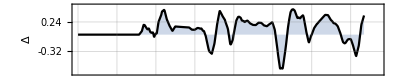
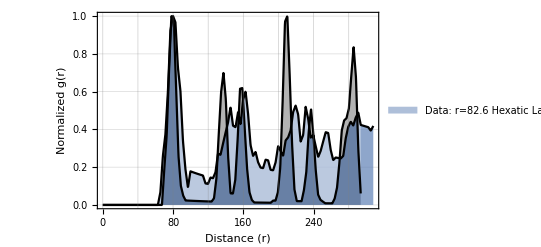
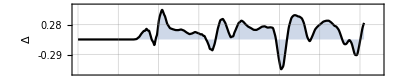
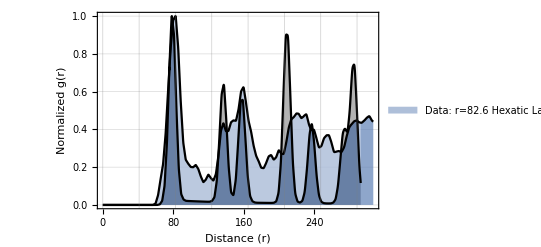

```mathematica
(*     Additional Option #4 - boots                                     *)
(*     Determines the Number of Randomized Displacements used to Smooth *)
(*     Default is 25                                                    *)
PlotPairCorrelationFunction[xylene2000,boots-> #]&/@{1,200}
```

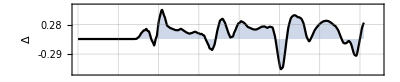
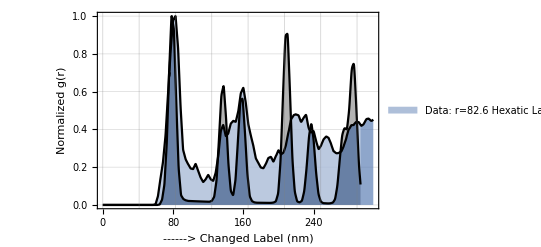

```mathematica
(*     Additional Option #5 - xLabel                    *)
(*     Change the x-axis label to have any string.      *)
PlotPairCorrelationFunction[xylene2000,xLabel->"------>  Changed Label (nm)"]
```

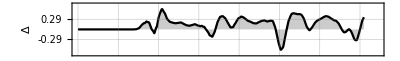
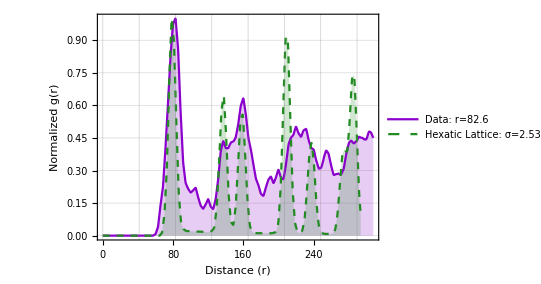
{-Graphics- | 
-Graphics- | }

```mathematica
(*     Additional Option #6 - stacked           *)
(*     Use the Green/Purple colour scheme.      *)
PlotPairCorrelationFunction[xylene2000,stacked->False]
```

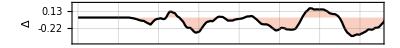
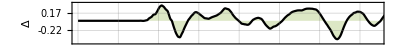
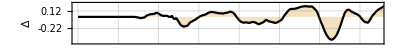
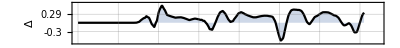
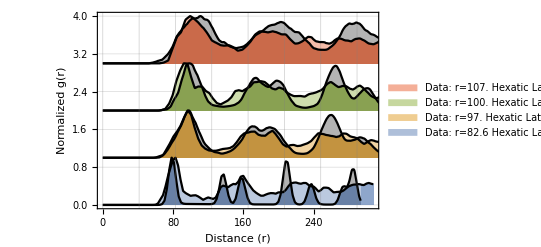

```mathematica
(*  Call in a List of Data:  *)
(* - Automatically detects multiple {x,y} data and plots it as a stack.  *)
(* - Residual functions at the top are Hexatic Lattice Substractions. *)
(* - All Options above work with this stacked version as well.  *)

PlotPairCorrelationFunction@xyXyleneList
```

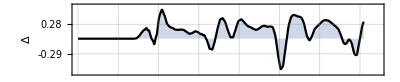
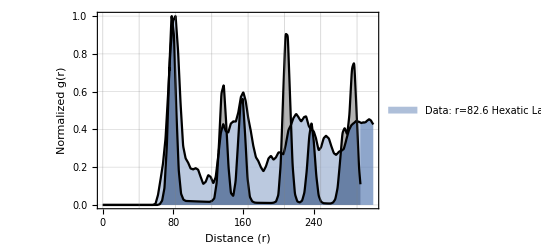
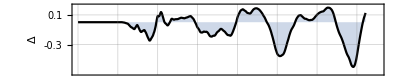
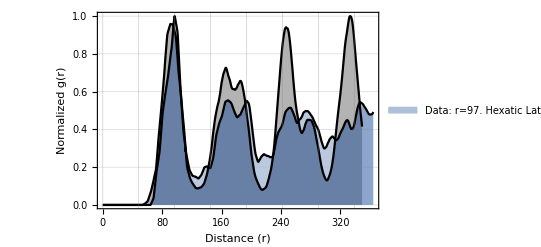
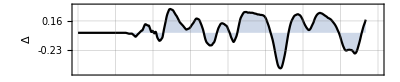
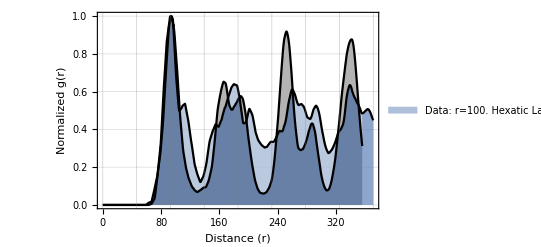
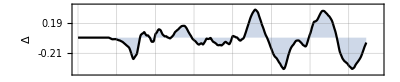
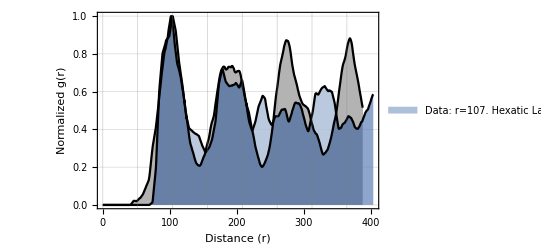

```mathematica
(*     MAP in a List of Data:    *)
(* Returns the Individual Plots for each Configuration in the List *)

(*    Note the:  "/@"  NOT  "@"      *)

PlotPairCorrelationFunction/@xyXyleneList
```

```mathematica
(*    Distance Estimation from: Mathematica's Nearest[] Function   *)

AverageFirstNeighbourDistance/@xyXyleneList
```

{71.3071,82.635,85.4448,89.7071}

```mathematica
(*    Distance Estimation from: First Peak of g(r) - (no smoothing here)  *)

FirstPeakValue/@(PairCorrelationFunction[#]&/@xyXyleneList)
```

{82.8435,96.5914,96.1881,103.78}

```mathematica
(*    Distance Estimation from: Voronoi Areas                      *)
(*    Returns:  { hexatic spacing,  lattice disorder parameter }  *)
ExpectedHexagonalDiameter/@xyXyleneList
```

{{82.6236,2.5267},{97.0426,7.45882},{100.223,6.63668},{107.439,11.4126}}

## Bond Order - Angular Orientation of Neighbours

```mathematica
(*  Extract the local bond order parameter for each particle *)
(*  Call using: the data and symmetry number   *)

bop=BondOrderParameter[xylene2000,6];
Mean[bop]
StandardDeviation[bop]
```

0.770507

0.142593

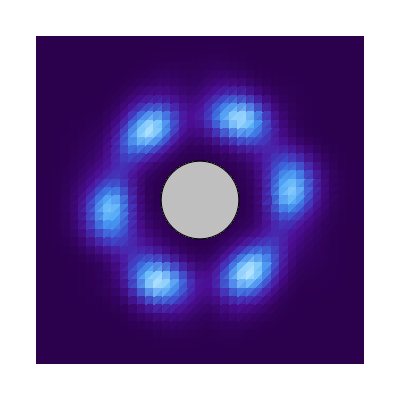
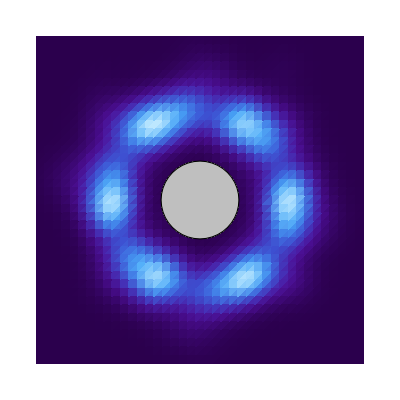
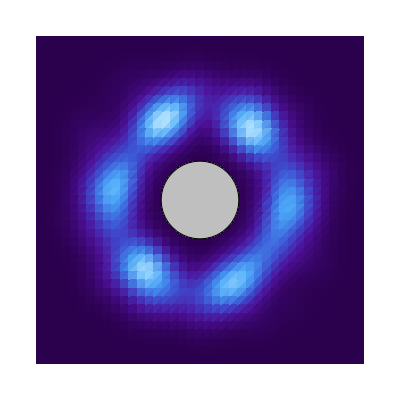
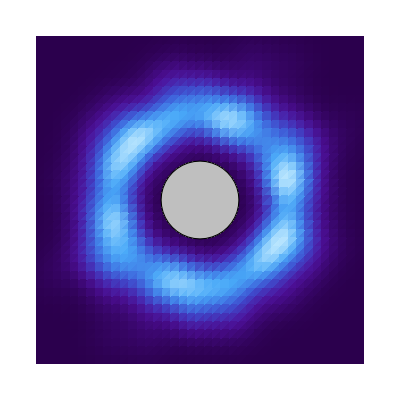

```mathematica
(* Coordination cloud shows the probability of Neighbours relative to each object *) 
(* Similar to the Fourier Transform, except it can be separated by Coordination   *)

(CoordinationNeighbourCloud/@xyXyleneList)[[All,2]]
```

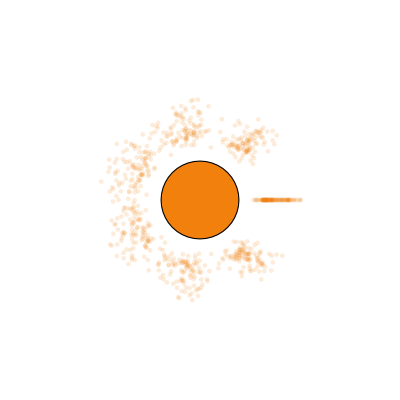
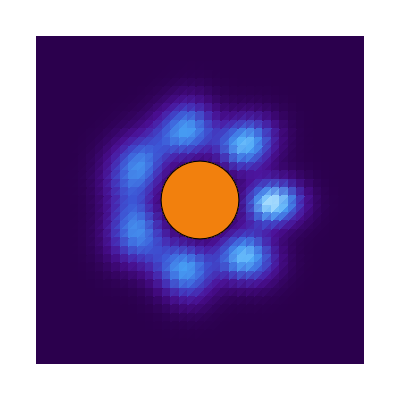
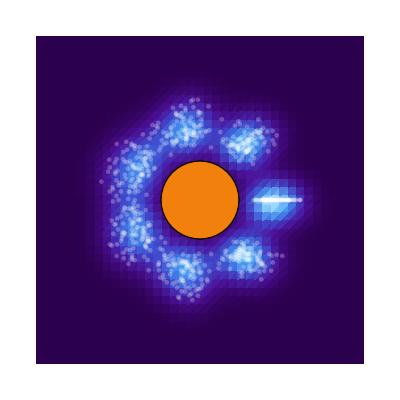

```mathematica
(*   Only select the particles that have 7 neighbours *)

CoordinationNeighbourCloud[xylene2000,coord->7]
```

## Diffraction - Correlation in Inverse Space

```mathematica
(*  Plots the Diffraction (Fourier Transform) using a combination of:  *)
(*   ...Mathematica's ImagePeriodogram and ADO FFT (below)  *)

GraphicsRow[DiffractionPatternFromPosition/@xyXyleneList,ImageSize->Large]
```

-Graphics-

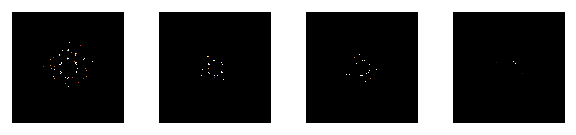

```mathematica
(*  Use older routine that ADO developed  *)

GraphicsRow[DiffractionPatternFromPosition[#,annulus-> False]&/@xyXyleneList,ImageSize->Large]
```